```mathematica
fApprox[z_]:=Normal[Series[f[z],{z,0,20}]]
gApprox[z_]:=Normal[Series[g[z],{z,0,20}]]
secondSeries=Sum[((-Sin[z]^2)/2)^k (x^k)/k!,{k,0,Infinity}]
```

```mathematica
nMax=20;
f[z_]:=(Sin[z])^2;
coef[n_,z_]:=Exp[2 I z]*Sum[(Sum[Binomial[1/2,k](-1)^(k+l)Binomial[k,l],{k,0,nMax}])*(((-f[z]/2)^(n-l))/(n-l)!),{l,0,n}]
```

```mathematica
cn[n_]:=NIntegrate[coef[n,z],{z,-Pi/2,Pi/2}]
```

```mathematica
Table[cn[n],{n,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.64545×10^-17-2.27682×10^-18 ⅈ and 6.18956×10^-17 for the integral and error estimates.

{2.64545×10^-17-2.27682×10^-18 ⅈ,0.049233,0.972351,-3.36233+0. ⅈ,12.0429,-37.0088+0. ⅈ,93.7841,-196.066+1.13687×10^-13 ⅈ,340.423,-494.031+0. ⅈ,602.082}

## Bekomen van de reeksontwikkeling

```mathematica
Lmax=5;
integrand[n_,y_]:=Sum[(((-4 y^2)^(n-l))/Factorial[2(n-l)])*Sum[(1/Factorial[j])*Sum[Product[((-1)^(nList[[i]]+3)*2^(2 nList[[i]])*y^(2 nList[[i]]+2))/Factorial[2 nList[[i]]+2],{i,1,j}],{nList,IntegerPartitions[l,{j}]}],{j,0,Lmax}],{l,0,n}]
integrand[5,20]
```

5325555473122918400000000/56133

```mathematica
n=1
```

1

```mathematica
NIntegrate[integrand[n,y],{y,-100,100}]
```

6.65333×10^8

```mathematica
f[y_,k_]:=Exp[-y^2/2]*Sum[((-4 y^2)^(k-l))/Factorial[2 (k-l)]*Sum[(1/Factorial[n])*Sum[Product[((-1)^(nList[[i]]+3)*2^(2 nList[[i]])*y^(2 nList[[i]]+2))/Factorial[2 nList[[i]]+2],{i,1,n}],{nList,IntegerPartitions[l,{n}]}],{n,0,l}],{l,0,k}];
```

```mathematica
b[n_]=NIntegrate[f[y,n],{y,-Infinity,Infinity}]
```

-3.75994

```mathematica
c[n_]:=Sqrt[2 Pi] Gamma[n+3/2]Gamma[n-1/2]2^n/(Gamma[3/2]Gamma[-1/2])
```

```mathematica
c[1]
```

-3 √(π/2)

{0,1,2,3,4,5,6,7,8,9,10}

{-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994,-3.75994}

{√(2 π),-3 √(π/2),-(15 √(π/2))/2,-(315 √(π/2))/4,-(14175 √(π/2))/8,-(1091475 √(π/2))/16,-(127702575 √(π/2))/32,-(21070924875 √(π/2))/64,-(4656674397375 √(π/2))/128,-(1327152203251875 √(π/2))/256,-(473793336560919375 √(π/2))/512}

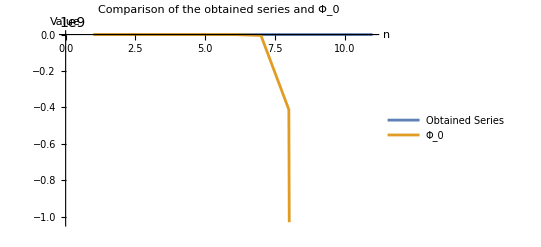

```mathematica
(*Maak een lijst van n-waarden*)nValues=Range[0,10]

(*Bereken b[n] en c[n] voor elke n*)
bValues=Table[b[n],{n,nValues}]
cValues=Table[c[n],{n,nValues}]

(*Maak de plot*)
ListLinePlot[{bValues,cValues},PlotLegends->{"Obtained Series","Φ_0"},AxesLabel->{"n","Value"},PlotLabel->"
Comparison of the obtained series and Φ_0"]
```

## Vergelijken van de reeksontwikkeling met exacte oplossing

```mathematica
besselFunction[lambda_]:=(Pi/Sqrt[lambda])*Exp[-1/(4 lambda)]*BesselI[1,1/(4 lambda)]
reeks0[n_,lambda_]:=Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
reeksPi[n_,lambda_]:=Exp[-1/(2 lambda)]Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((-2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
reeksTotaal[n_,lambda_]:=reeks0[n,lambda]+reeksPi[n,lambda]
```

General::munfl: Exp[-17482.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-34965.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

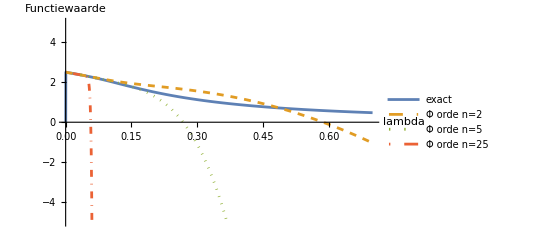

```mathematica
Plot[{besselFunction[lambda],reeksTotaal[2,lambda],reeksTotaal[5,lambda],reeksTotaal[25,lambda]},{lambda,0,0.7},PlotLegends->{"exact","Φ order n=2","Φ order n=5","Φ order n=25"},PlotStyle->{Automatic,Dashed,Dotted,DotDashed},AxesLabel->{"lambda","Function value"},PlotRange->{{0,0.7},{-5,5}}]
```

```mathematica
Export["VergelijkingOrdesPhi.pdf",Plot[{besselFunction[lambda],reeksTotaal[2,lambda],reeksTotaal[5,lambda],reeksTotaal[25,lambda]},{lambda,0,0.7},PlotLegends->{"exact","Φ order n=2","Φ order n=5","Φ order n=25"},PlotStyle->{Automatic,Dashed,Dotted,DotDashed},AxesLabel->{"lambda","Function value"},PlotRange->{{0,0.7},{-5,5}}]]
```

General::munfl: Exp[-17482.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-34965.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

VergelijkingOrdesPhi.pdf

## Optimal Truncation

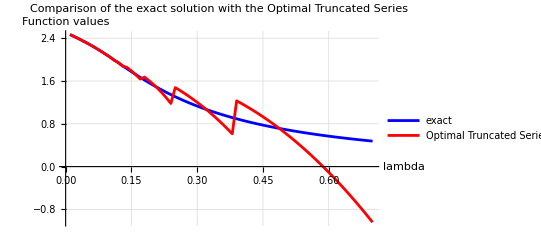

```mathematica
(*Foutfunctie*)errorFunction[n_,lambda_]:=Abs[besselFunction[lambda]-reeksTotaal[n,lambda]]

(*Optimale truncatiepunt vinden*)
findOptimalN[lambda_]:=Module[{n,minError,optimalN},minError=Infinity;
optimalN=0;
For[n=0,n<=25,n++,If[errorFunction[n,lambda]<minError,minError=errorFunction[n,lambda];
optimalN=n;];];
optimalN]

(*Data genereren voor plotten*)
lambdaValues=Range[0.01,0.7,0.01];
exactValues=besselFunction/@lambdaValues;
optimalNValues=findOptimalN/@lambdaValues;
approxValues=Table[reeksTotaal[optimalNValues[[i]],lambdaValues[[i]]],{i,Length[lambdaValues]}];

(*Resultaten plotten*)
ListLinePlot[{Transpose[{lambdaValues,exactValues}],Transpose[{lambdaValues,approxValues}]},PlotLegends->{"exact","Optimal Truncated Series"},PlotStyle->{Blue,Red,Dashed},AxesLabel->{"lambda","Function values"},PlotRange->{{0,0.7},Automatic},GridLines->Automatic,PlotLabel->"Comparison of the exact solution with the Optimal Truncated Series"]
```

```mathematica
Export["comparisonExactSolutionOptimalTruncated.pdf",ListLinePlot[{Transpose[{lambdaValues,exactValues}],Transpose[{lambdaValues,approxValues}]},PlotLegends->{"exact","Optimal Truncated Series"},PlotStyle->{Blue,Red,Dashed},AxesLabel->{"lambda","Function values"},PlotRange->{{0,0.7},Automatic},GridLines->Automatic,PlotLabel->"Comparison of the exact solution with the Optimal Truncated Series"]]
```

comparisonExactSolutionOptimalTruncated.pdf

## Kleine Lambda

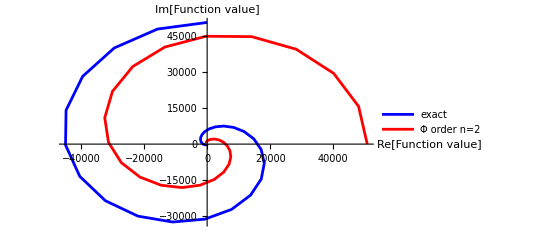

```mathematica
lambdaAbs=0.05;
thetaRange=Table[theta,{theta,0,Pi,Pi/100}];
lambdaValues=lambdaAbs*Exp[I*thetaRange];

besselValues=besselFunction[#]&/@lambdaValues;
reeksValues=reeksTotaal[2,#]&/@lambdaValues;

ListLinePlot[{Transpose[{Re[besselValues],Im[besselValues]}],Transpose[{Re[reeksValues],Im[reeksValues]}]},PlotLegends->{"exact","Φ order n=2"},AxesLabel->{"Re[Function value]","Im[Function value]"},PlotStyle->{Blue,Red},PlotRange->All]
```

```mathematica
Export["VergelijkingImaginaireWaarden.pdf",ListLinePlot[{Transpose[{Re[besselValues],Im[besselValues]}],Transpose[{Re[reeksValues],Im[reeksValues]}]},PlotLegends->{"exact","Φ order n=2"},AxesLabel->{"Re[Function value]","Im[Function value]"},PlotStyle->{Blue,Red},PlotRange->All]]
```

VergelijkingImaginaireWaarden.pdf

## Trans - series

Nog niet in orde

```mathematica
reeks0[n_,lambda_]:=Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
reeksPi[n_,lambda_]:=Exp[-1/(2 lambda)]Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((-2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
o[n_,lambda_]:=reeks0[n,lambda]+I*Exp[-1/(2 lambda)]*reeksPi[n,lambda]
Integrand[n_,lambda_,z_]:=Exp[- lambda z]* o[n,z]
```

```mathematica
resummation[n_,lambda_]:=Re[NIntegrate[Integrand[n,lambda,z],{z,0,1-I/2}]+NIntegrate[Integrand[n,lambda,z],{z,1-I/2,Infinity-I/2}]]
```

```mathematica
besselFunction[lambda_]:=(Pi/Sqrt[lambda])*Exp[-1/(4 lambda)]*BesselI[1,1/(4 lambda)];
```

```mathematica
Plot[{resummation[2,lambda],resummation[5,lambda],resummation[25,lambda],besselFunction[lambda]},{lambda,0.1,15},PlotRange->All,PlotLabels->{"n=2","n=5","n=25","Bessel"},PlotStyle->{Blue,Red,Green,Black},AxesLabel->{"lambda","Function Value"},PlotLegends->"Expressions"]
```

$Aborted

```mathematica
(*Waarden voor lambda*)lambdaValues=Range[0.5,15,0.5];

(*Tabel genereren*)
table=Table[{lambda,resummation[2,lambda],resummation[5,lambda],resummation[25,lambda],besselFunction[lambda]},{lambda,lambdaValues}];

(*Tabel weergeven*)
Grid[Prepend[table,{"λ","resummation[2, λ]","resummation[5, λ]","resummation[25, λ]","Bessel"}],Frame->All,Alignment->Center]
```

## Opnieuw

```mathematica
besselFunction[lambda_]:=(Pi/Sqrt[lambda])*Exp[-1/(4 lambda)]*BesselI[1,1/(4 lambda)]
borelSeries0[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,2  lambda];
borelSeriesPi[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,-2 lambda];
```

```mathematica
resummation[lambda_]:=Re[NIntegrate[(1/lambda)Exp[-z/ lambda]borelSeries0[z],{z,0,Infinity-(1/10)I}]+I Exp[-1/(2 lambda)] * NIntegrate[(1/lambda)Exp[-z /lambda]borelSeriesPi[z],{z,0,Infinity-(1/10)I}]]
```

```mathematica
resummation[lambda_]:=(Re[NIntegrate[(1/lambda)Exp[-z/ lambda]borelSeries0[z],{z,0,Infinity-(1/10)I}]+I Exp[-1/(2 lambda)] * NIntegrate[(1/lambda)Exp[-z /lambda]borelSeriesPi[z],{z,0,Infinity-(1/10)I}]]+Re[NIntegrate[(1/lambda)Exp[-z/ lambda]borelSeries0[z],{z,0,Infinity+(1/10)I}]+I Exp[-1/(2 lambda)] * NIntegrate[(1/lambda)Exp[-z /lambda]borelSeriesPi[z],{z,0,Infinity+(1/10)I}]])/2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 2.05234+0.0191502 ⅈ and 0.0000615582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 2.05234+0.0191502 ⅈ and 0.0000615582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 0.569252+1.76912 ⅈ and 0.00070422 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

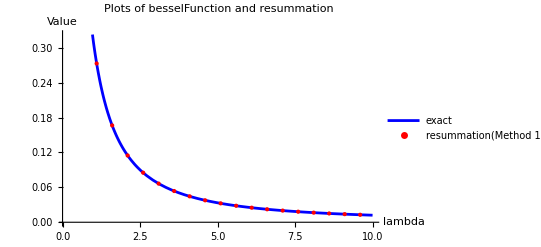

```mathematica
(*Genereer data voor scatterplot*)lambdaValues=Table[lambda,{lambda,1/10,10,1/2}];
resummationValues=Table[resummation[lambda],{lambda,lambdaValues}];

(*Plot de functies*)
Show[Plot[besselFunction[lambda],{lambda,1/10,10},PlotLegends->{"exact"},PlotStyle->Blue,AxesLabel->{"lambda","Value"},PlotLabel->"Plots of besselFunction and resummation"],ListPlot[Transpose[{lambdaValues,resummationValues}],PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"resummation(Method 1)"}]]
```

```mathematica
Export["ResultResummationMethod2.pdf",Show[Plot[besselFunction[lambda],{lambda,1/10,10},PlotLegends->{"exact"},PlotStyle->Blue,AxesLabel->{"lambda","Value"},PlotLabel->"Plots of besselFunction and resummation"],ListPlot[Transpose[{lambdaValues,resummationValues}],PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"resummation(Method 2)"}]]]
```

ResultResummationMethod2.pdf

## Vergelijking van de Methoden

```mathematica
besselFunction[lambda_]:=(Pi/Sqrt[lambda])*Exp[-1/(4 lambda)]*BesselI[1,1/(4 lambda)]
reeks0[n_,lambda_]:=Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
reeksPi[n_,lambda_]:=Exp[-1/(2 lambda)]Sqrt[2 Pi]Sum[Gamma[l+3/2]Gamma[l-1/2]((-2 lambda)^l)/(Gamma[3/2]Gamma[-1/2]Factorial[l]),{l,0,n}]
reeksTotaal[n_,lambda_]:=reeks0[n,lambda]+reeksPi[n,lambda]
borelSeries0[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,2  lambda];
borelSeriesPi[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,-2 lambda];
```

```mathematica
resummation[lambda_]:=Re[NIntegrate[(1/lambda)Exp[-z/ lambda]borelSeries0[z],{z,0,Infinity-(1/10)I}]+I Exp[-1/(2 lambda)] * NIntegrate[(1/lambda)Exp[-z /lambda]borelSeriesPi[z],{z,0,Infinity-(1/10)I}]]
```

```mathematica
lambdaValues=Table[lambda,{lambda,1/10,10,0.5}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 2.05234+0.0191502 ⅈ and 0.0000615582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 0.569252+1.76912 ⅈ and 0.00070422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.497111}. NIntegrate obtained 0.272979+3.15945 ⅈ and 0.000754701 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

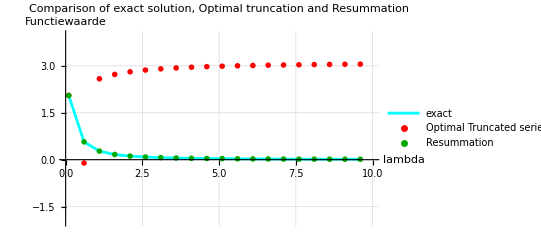

```mathematica
(*Exacte Bessel-functie*)besselFunction[lambda_]:=(Pi/Sqrt[lambda])*Exp[-1/(4 lambda)]*BesselI[1,1/(4 lambda)]

(*Reeksbenaderingen*)
reeks0[n_,lambda_]:=Sqrt[2 Pi] Sum[Gamma[l+3/2] Gamma[l-1/2] ((2 lambda)^l)/(Gamma[3/2] Gamma[-1/2] Factorial[l]),{l,0,n}]

reeksPi[n_,lambda_]:=Exp[-1/(2 lambda)] Sqrt[2 Pi] Sum[Gamma[l+3/2] Gamma[l-1/2] ((-2 lambda)^l)/(Gamma[3/2] Gamma[-1/2] Factorial[l]),{l,0,n}]

reeksTotaal[n_,lambda_]:=reeks0[n,lambda]+reeksPi[n,lambda]

(*Foutfunctie*)
errorFunction[n_,lambda_]:=Abs[besselFunction[lambda]-reeksTotaal[n,lambda]]

(*Optimale truncatiepunt vinden*)
findOptimalN[lambda_]:=Module[{n,minError,optimalN},minError=Infinity;
optimalN=0;
For[n=0,n<=25,n++,If[errorFunction[n,lambda]<minError,minError=errorFunction[n,lambda];
optimalN=n;];];
optimalN]

(*Borel-series en resummatie*)
borelSeries0[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,2 lambda]
borelSeriesPi[lambda_]:=Sqrt[2 Pi] Hypergeometric2F1[3/2,-1/2,1,-2 lambda]

resummation[lambda_]:=Re[NIntegrate[(1/lambda) Exp[-z/lambda] borelSeries0[z],{z,0,Infinity-(1/10) I}]+I Exp[-1/(2 lambda)]*NIntegrate[(1/lambda) Exp[-z/lambda] borelSeriesPi[z],{z,0,Infinity-(1/10) I}]]

(*Lambda-waarden*)
lambdaValues=Table[lambda,{lambda,1/10,10,0.5}];
exactValues=besselFunction/@lambdaValues;
optimalNValues=findOptimalN/@lambdaValues;
optimalTruncationValues=Table[reeksTotaal[optimalNValues[[i]],lambdaValues[[i]]],{i,Length[lambdaValues]}];
resummationValues=resummation/@lambdaValues;

(*Resultaten plotten*)
Show[ListLinePlot[Transpose[{lambdaValues,exactValues}],PlotStyle->{Cyan},PlotLegends->{"exact"},AxesLabel->{"lambda","Functiewaarde"},PlotRange->{{0,10},{-2,4}},GridLines->Automatic],ListPlot[{Transpose[{lambdaValues,optimalTruncationValues}],Transpose[{lambdaValues,resummationValues}]},PlotStyle->{Red,Darker[Green]},PlotMarkers->{Style["o",12],Style["x",12]},PlotLegends->{"Optimal Truncated series","Resummation"}],PlotLabel->"Comparison of exact solution, Optimal truncation and Resummation"]
```

```mathematica
Export["ComparisonExactSolutionOptimalTruncationResurgence.pdf",Show[ListLinePlot[Transpose[{lambdaValues,exactValues}],PlotStyle->{Cyan},PlotLegends->{"exact"},AxesLabel->{"lambda","Function value"},PlotRange->{{0,10},{-2,4}},GridLines->Automatic],ListPlot[{Transpose[{lambdaValues,optimalTruncationValues}],Transpose[{lambdaValues,resummationValues}]},PlotStyle->{Red,Darker[Green]},PlotMarkers->{Style["o",12],Style["x",12]},PlotLegends->{"Optimal Truncated series","Resummation"}],PlotLabel->"Comparison of exact solution, Optimal truncation and Resummation"]]
```

ComparisonExactSolutionOptimalTruncationResurgence.pdf